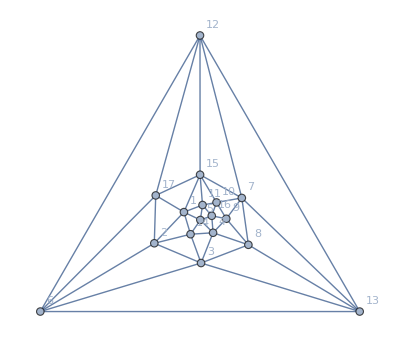

```mathematica
plantri8
```

```mathematica
Length[plantri]
```

100000

```mathematica
Graph[Sort[Subgraph[Graph[Sort[vars,CompareSymbols],edges1],{v13x2x4x5,v13x24x5,v13x25x4,v1x24x3x5,v1x25x3x4,v1x24x35,v14x25x3,v1x2x35x4,v14x2x3x5,v14x2x35}]//EdgeList//Tally,#1[[2]]<#2[[2]]&]]
```

```mathematica
myedges={{v14x2x35<->v1x24x35,64},{v14x25x3<->v14x2x35,64},{v13x25x4<->v14x2x35,64},{v13x24x5<->v14x2x35,64},{v13x2x4x5<->v14x2x3x5,64},{v14x2x3x5<->v1x24x3x5,64},{v13x2x4x5<->v1x2x35x4,64},{v1x25x3x4<->v1x2x35x4,64},{v14x25x3<->v1x24x35,64},{v13x25x4<->v14x25x3,64},{v13x24x5<->v14x25x3,64},{v13x25x4<->v1x24x35,64},{v13x24x5<->v1x24x35,64},{v1x24x3x5<->v1x25x3x4,64},{v13x24x5<->v13x25x4,64},{v13x2x4x5<->v14x2x35,96},{v14x2x35<->v1x24x3x5,96},{v14x2x35<->v1x25x3x4,96},{v14x2x3x5<->v1x24x35,96},{v13x25x4<->v14x2x3x5,96},{v13x24x5<->v14x2x3x5,96},{v14x25x3<->v1x2x35x4,96},{v13x25x4<->v1x2x35x4,96},{v13x24x5<->v1x2x35x4,96},{v13x2x4x5<->v14x25x3,96},{v14x25x3<->v1x24x3x5,96},{v13x2x4x5<->v1x24x35,96},{v1x24x35<->v1x25x3x4,96},{v13x24x5<->v1x25x3x4,96},{v13x25x4<->v1x24x3x5,96},{v14x2x3x5<->v1x25x3x4,128},{v14x2x3x5<->v1x2x35x4,128},{v1x24x3x5<->v1x2x35x4,128},{v13x2x4x5<->v1x25x3x4,128},{v13x2x4x5<->v1x24x3x5,128}}
```

{{v14x2x35<->v1x24x35,64},{v14x25x3<->v14x2x35,64},{v13x25x4<->v14x2x35,64},{v13x24x5<->v14x2x35,64},{v13x2x4x5<->v14x2x3x5,64},{v14x2x3x5<->v1x24x3x5,64},{v13x2x4x5<->v1x2x35x4,64},{v1x25x3x4<->v1x2x35x4,64},{v14x25x3<->v1x24x35,64},{v13x25x4<->v14x25x3,64},{v13x24x5<->v14x25x3,64},{v13x25x4<->v1x24x35,64},{v13x24x5<->v1x24x35,64},{v1x24x3x5<->v1x25x3x4,64},{v13x24x5<->v13x25x4,64},{v13x2x4x5<->v14x2x35,96},{v14x2x35<->v1x24x3x5,96},{v14x2x35<->v1x25x3x4,96},{v14x2x3x5<->v1x24x35,96},{v13x25x4<->v14x2x3x5,96},{v13x24x5<->v14x2x3x5,96},{v14x25x3<->v1x2x35x4,96},{v13x25x4<->v1x2x35x4,96},{v13x24x5<->v1x2x35x4,96},{v13x2x4x5<->v14x25x3,96},{v14x25x3<->v1x24x3x5,96},{v13x2x4x5<->v1x24x35,96},{v1x24x35<->v1x25x3x4,96},{v13x24x5<->v1x25x3x4,96},{v13x25x4<->v1x24x3x5,96},{v14x2x3x5<->v1x25x3x4,128},{v14x2x3x5<->v1x2x35x4,128},{v1x24x3x5<->v1x2x35x4,128},{v13x2x4x5<->v1x25x3x4,128},{v13x2x4x5<->v1x24x3x5,128}}

```mathematica
Map[First,myedges]//VertexList
```

{v14x2x35,v1x24x35,v14x25x3,v13x25x4,v13x24x5,v13x2x4x5,v14x2x3x5,v1x24x3x5,v1x2x35x4,v1x25x3x4}

```mathematica
128/32
```

4

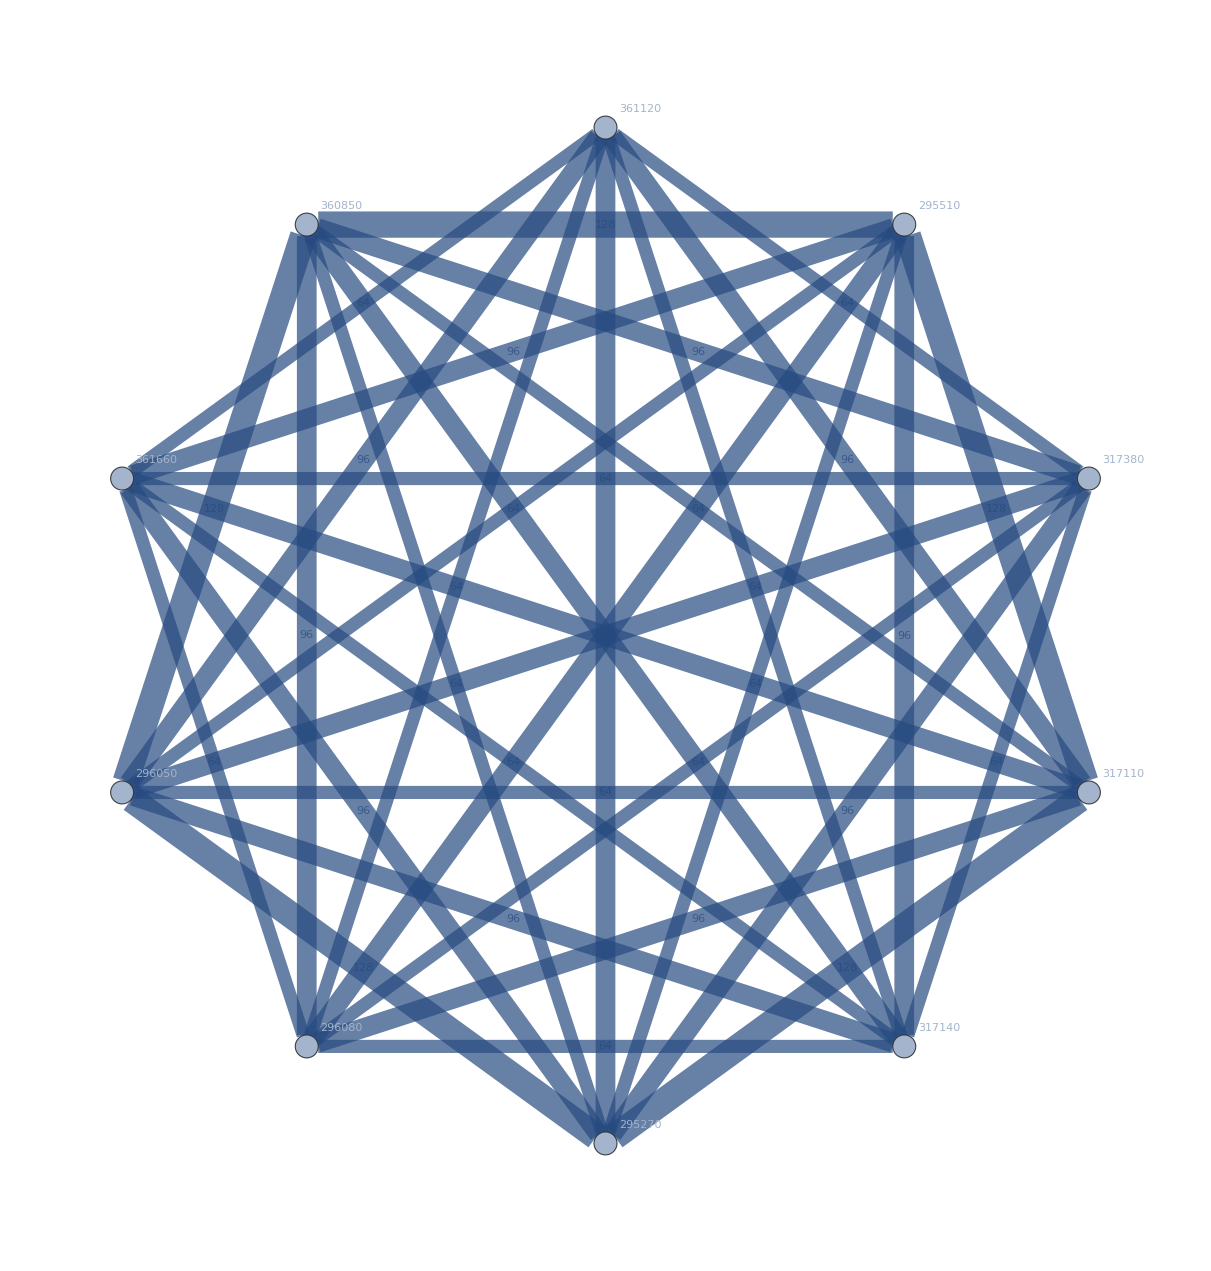

```mathematica
Graph[{v13x2x4x5,v13x24x5,v1x24x3x5,v1x24x35,v1x2x35x4,v14x2x35,v14x2x3x5,v14x25x3,v1x25x3x4,v13x25x4},Map[Labeled[#[[1]],Framed[Style[#[[2]],16,Red,Bold],Background->White]]&,myedges],EdgeStyle->Map[#[[1]]->Thickness[#[[2]]/2^13]&,myedges],VertexLabels->Table[k->(k/.RepGraph["C"]),{k,Map[First,myedges]//VertexList}],GraphLayout->"CircularEmbedding"]
```